# Simple 2D Ising Model renormalization

Giuseppe D’Auria

Latest changes: 23/08/04 05:06 p.m.

In this Notebook, we explore two dimensional Ising model and perform  Kadanoff’ s renormalization group theory for 2 D lattices.

## Definition of the 2D Ising model

We define the isingModel2D function to generate an initial random configuration of a 2 D magnetic (or spin) system,where L is the grid size. of the lattice. The configuration is represented as a 2 D matrix of dimension LxL, initialized as a random LxL matrix of 1 and -1, which is returned by the function as “config”.

```mathematica
isingModel2D[L_]:=Module[{config},config=RandomChoice[{-1,1},{L,L}];
Return[config];];
```

## Definition of the renormalizing function

```mathematica
renormalize2D[config_]:=Module[{L,newConfig},L=Length[config];
newConfig=Table[config[[i,j]] config[[i,j+1]] config[[i+1,j]] config[[i+1,j+1]],{i,1,L,2},{j,1,L,2}];
Return[newConfig];];
```

The renormalize2D function performs renormalization of a 2D configuration using Kadanoff’s method.
Function input parameters : The renormalise2D function accepts a single input parameter, config, which represents the configuration of the 2 D lattice to be renormalized.

The main step of the function is the renormalization of the configuration. 
To do this, we use a double iteration on i and j in increments of 2, which allows us to consider only the lattice sites at distance 2. From the spin values at the sites config[[i,j]], config[[i,j+1]], config[[i+1,j]] and config[[i+1,j+1]], we compute the product of their spin values to obtain a new spin value in the new configuration newConfig.
At the end of the renormalization process, the function returns the new configuration newConfig, which is a 2D array with dimensions halved from the initial configuration.

## Numerical Example

In the numerical example, we generate an initial random configuration initialConfig2D using the model isingModel2D, then apply the renormalize2D function to this configuration to obtain renormalizedConfig2D1. Finally, we visualize the initial configuration and the renormalized configurations using ArrayPlot graphs.

### Generate a random initial configuration with L = 256

```mathematica
initialConfig2D=isingModel2D[256];
```

```mathematica
(*Print the initial configuration (if you want)*)
(*CellPrint[TextCell["Initial Configuration:","Subsubtitle"]]
MatrixForm[initialConfig2D]*)
```

### Renormalize the configuration

```mathematica
renormalizedConfig2D1=renormalize2D[initialConfig2D];
(*Print the renormalized configuration (if you want)*)
(*CellPrint[TextCell["Renormalized Configuration:","Subsubtitle"]]
MatrixForm[renormalizedConfig2D]*)
```

We also perform further steps of the renormalization flow to probe how the lattice evolves at each step

```mathematica
renormalizedConfig2D2=renormalize2D[renormalizedConfig2D1];
renormalizedConfig2D3=renormalize2D[renormalizedConfig2D2];
renormalizedConfig2D4=renormalize2D[renormalizedConfig2D3];
renormalizedConfig2D5=renormalize2D[renormalizedConfig2D4];
```

### Configuration Plots

#### Plot of the initial configuration

```mathematica
plotInitialConfig2D=ArrayPlot[initialConfig2D,ColorRules->{-1->Red,1->Blue},PlotLabel->"Initial Configuration",ImageSize->300];
```

#### Plot of the renormalized configurations

```mathematica
plotRenormalizedConfig2D1=ArrayPlot[renormalizedConfig2D1,ColorRules->{-1->Red,1->Blue},PlotLabel->"Step 1 Renormalized Configuration",ImageSize->300];
plotRenormalizedConfig2D2=ArrayPlot[renormalizedConfig2D2,ColorRules->{-1->Red,1->Blue},PlotLabel->"Step 2 Renormalized Configuration",ImageSize->300];
plotRenormalizedConfig2D3=ArrayPlot[renormalizedConfig2D3,ColorRules->{-1->Red,1->Blue},PlotLabel->"Step 3 Renormalized Configuration",ImageSize->300];
plotRenormalizedConfig2D4=ArrayPlot[renormalizedConfig2D4,ColorRules->{-1->Red,1->Blue},PlotLabel->"Step 4 Renormalized Configuration",ImageSize->300];
plotRenormalizedConfig2D5=ArrayPlot[renormalizedConfig2D5,ColorRules->{-1->Red,1->Blue},PlotLabel->"Step 5 Renormalized Configuration",ImageSize->300];
```

Display the plots side by side

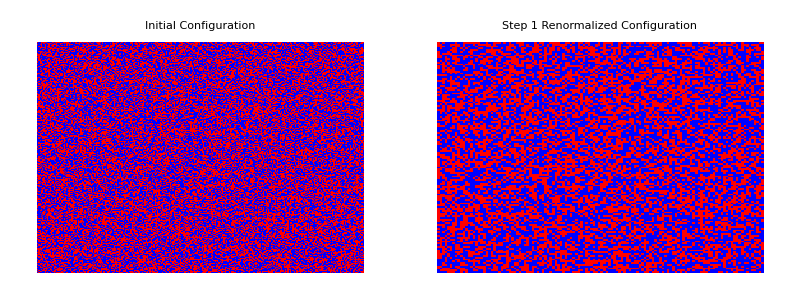

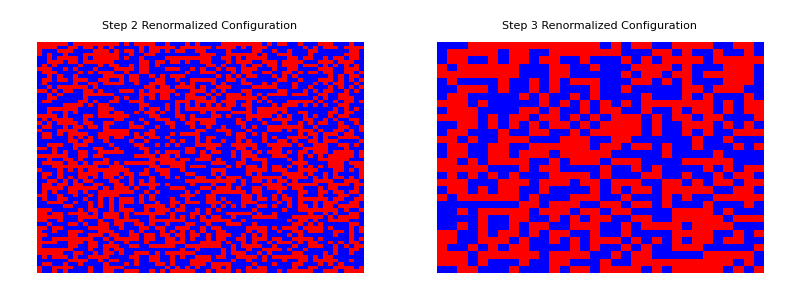

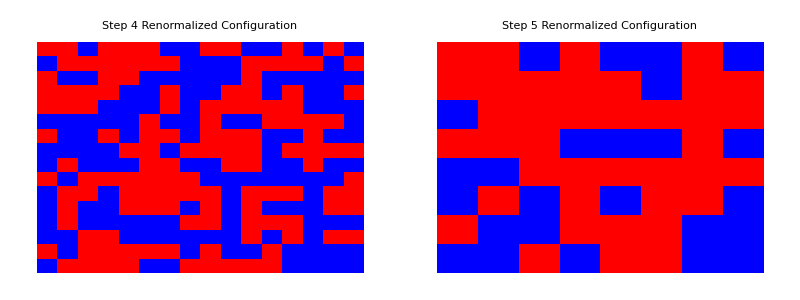

```mathematica
CellPrint[ExpressionCell[Grid[{{plotInitialConfig2D,plotRenormalizedConfig2D1}},Spacings->{1,1}],"Output"]]
CellPrint[ExpressionCell[Grid[{{plotRenormalizedConfig2D2,plotRenormalizedConfig2D3}},Spacings->{1,1}],"Output"]]
CellPrint[ExpressionCell[Grid[{{plotRenormalizedConfig2D4,plotRenormalizedConfig2D5}},Spacings->{1,1}],"Output"]]
```

In the output, you can see several graphs side by side : one for the initial 2 D configuration and the others for the renormalized configuration at each step.The initial configuration is random, while the renormalized configurations at each step are obtained by applying the Kadanoff renormalization function to the initial 2 D Ising model.